```mathematica
Quit[]  (*To clean your kernel before a fresh, full run of the notebook*)
```

# COFLASY-M: COsmological evolution of FLAvour ASYmmetries - Mathematica

```mathematica
(*Last major update: 09-01-2024*)

(*Please refer to Lepton Flavour Asymmetries: From the very early Universe to BBN, Valerie Domcke, Miguel Escudero, Mario Fernández Navarro, Stefan Sandner, [2501.XXXXXX] ... to be added*)

(*Running the full notebook takes around 18 minutes in my laptop*)
(*Note that you should enable dynamic updating in order to properly visualise some content in this notebook*)
```

```mathematica
ti=Now;
```

## Fundamental equations, definitions and functions to solve

## Preliminaries

```mathematica
(*These are all constants to be used later*)

MeV=1;
GeV=10^3 MeV;
eV=10^-6 MeV;
MPr=2.435*10^18 GeV; (*reduced Planck mass*)
GF=1.166 10^-11 MeV;
MW=80.377 GeV;
SW2=0.223;(*squared sine of the weak mixing angle*)
me = 0.511MeV;
mμ=105.7MeV;

(*Mixing parameters used in the paper*)
Δmsq21=7.53*10^-5 eV^2;
Δmsq31=2.534*10^-3 eV^2; (*For inverted ordering, add minus sign*)
θ12=0.587;
θ23=0.831;
θ13=0.148;

δCP=0.0;(*This may be modified by the user but typically has small impact on the final results*)

FACΔn=1; (*Controls globally the overall normalization of asymmetries Δn=FACΔn(n-nbar)/T^3*)
```

```mathematica
(*These are useful functions to be used later*)

Commutator[A_,B_]:=A.B-B.A;
GellMannMatrices={({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}}),({{0, -I, 0}, {I, 0, 0}, {0, 0, 0}}),({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}}),({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}}),({{0, 0, -I}, {0, 0, 0}, {I, 0, 0}}),({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}}),({{0, 0, 0}, {0, 0, -I}, {0, I, 0}}),1/(√3)({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}})};

(*Structure constants of SU(3), fabc = 1/(4I)Tr(λa[λb,λc]), with λa being Gell-Mann matrices*)
fabc[a_,b_,c_]:=1/(4I)Tr[GellMannMatrices[[a]].Commutator[GellMannMatrices[[b]],GellMannMatrices[[c]]]];
(*Cross product generalised to dimension 8*)

Cross8[A_,B_]:={Sum[fabc[1,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}],Sum[fabc[2,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}],Sum[fabc[3,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}],Sum[fabc[4,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}],Sum[fabc[5,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}],Sum[fabc[6,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}],Sum[fabc[7,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}],Sum[fabc[8,b,c]A[[b]]B [[c]],{b,1,8},{c,1,8}]};

Unitmat=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});

(*This function is used to expand any given matrix in the basis of GellMann matrices and the identity matrix, note the 1/3 and 1/2 factors given our convention as in Eq. (22)*)

GellMannExpansion[a0_,a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_]:=1/3 a0*IdentityMatrix[3]+1/2(a1*GellMannMatrices[[1]]+a2*GellMannMatrices[[2]]+a3*GellMannMatrices[[3]]+a4*GellMannMatrices[[4]]+a5*GellMannMatrices[[5]]+a6*GellMannMatrices[[6]]+a7*GellMannMatrices[[7]]+a8*GellMannMatrices[[8]]);

GellMannComponents[X_]:=FullSimplify[Solve[GellMannExpansion[a0,a1,a2,a3,a4,a5,a6,a7,a8]==X,{a0,a1,a2,a3,a4,a5,a6,a7,a8}]]//First;
```

## Equations

```mathematica
(*Our goal is to write Eq. (25) from the notes*)

Clear[r0,r1,r2,r3,r4,r5,r6,r7,r8,rbar0,rbar1,rbar2,rbar3,rbar4,rbar5,rbar6,rbar7,rbar8];

OverDot[r⃗]=(OverVector[h0]+OverVector[vc])×r⃗ +vs r⃗×OverVector[r̄] + OverVector[Coll]; //Quiet
OverDot[OverVector[r̄]]=-(OverVector[h0]+OverVector[vc])×OverVector[r̄]+vs r⃗×OverVector[r̄] +OverVector[OverBar[Coll]]; //Quiet

Subscript[ṙ, 0]=Subscript[Coll, 0];//Quiet
Subscript[OverDot[r̄], 0]=Subscript[OverBar[Coll], 0];//Quiet

r⃗={r1,r2,r3,r4,r5,r6,r7,r8};
OverVector[r̄] ={rbar1,rbar2,rbar3,rbar4,rbar5,rbar6,rbar7,rbar8};

(*Density matrices*)

rmat=1/3 r0*IdentityMatrix[3]+1/2 r⃗ . GellMannMatrices;(*Eq. (22)*)
OverBar[rmat]=1/3 rbar0*IdentityMatrix[3]+1/2 OverVector[r̄]. GellMannMatrices;

rmat//MatrixForm
OverBar[rmat]//MatrixForm
rmat-OverBar[rmat]//MatrixForm
FullSimplify[Tr[rmat+OverBar[rmat]]]

(*stictly speaking the full density matrices are ρ=fFD(ξ=0)*r and ρ̄=fFD(ξ=0)*r̄) given our ansatz*)
```

(r0/3+1/2 (r3+r8/(√3)) | 1/2 (r1-ⅈ r2) | 1/2 (r4-ⅈ r5)
1/2 (r1+ⅈ r2) | r0/3+1/2 (-r3+r8/(√3)) | 1/2 (r6-ⅈ r7)
1/2 (r4+ⅈ r5) | 1/2 (r6+ⅈ r7) | r0/3-r8/(√3))

(rbar0/3+1/2 (rbar3+rbar8/(√3)) | 1/2 (rbar1-ⅈ rbar2) | 1/2 (rbar4-ⅈ rbar5)
1/2 (rbar1+ⅈ rbar2) | rbar0/3+1/2 (-rbar3+rbar8/(√3)) | 1/2 (rbar6-ⅈ rbar7)
1/2 (rbar4+ⅈ rbar5) | 1/2 (rbar6+ⅈ rbar7) | rbar0/3-rbar8/(√3))

(r0/3+1/2 (r3+r8/(√3))-rbar0/3+1/2 (-rbar3-rbar8/(√3)) | 1/2 (r1-ⅈ r2)+1/2 (-rbar1+ⅈ rbar2) | 1/2 (r4-ⅈ r5)+1/2 (-rbar4+ⅈ rbar5)
1/2 (r1+ⅈ r2)+1/2 (-rbar1-ⅈ rbar2) | r0/3+1/2 (-r3+r8/(√3))-rbar0/3+1/2 (rbar3-rbar8/(√3)) | 1/2 (r6-ⅈ r7)+1/2 (-rbar6+ⅈ rbar7)
1/2 (r4+ⅈ r5)+1/2 (-rbar4-ⅈ rbar5) | 1/2 (r6+ⅈ r7)+1/2 (-rbar6-ⅈ rbar7) | r0/3-r8/(√3)-rbar0/3+rbar8/(√3))

r0+rbar0

```mathematica
Tref=me; (*This is a reference temperature used to build the dimensionless variable x=Tref/T. Tref=me is a common convention, but other values such as Tref=10 MeV may be used*)

gs=2+4 7/8+7/8(r0+rbar0); (*Effective number of degrees of freedom, Eq. (10)*)
H[x_]:=√gs π/(√90 MPr)(Tref/x)^2; (*Hubble parameter, Eq. (9)*)


(*Note that the following terms correspond to the various contributions of Eq. (13)*)

(*H0: vaccuum oscillations*)
uUnitary=({{1, 0, 0}, {0, Cos[θ23], Sin[θ23]}, {0, -Sin[θ23], Cos[θ23]}}).({{Cos[θ13], 0, Sin[θ13]Exp[-I δCP]}, {0, 1, 0}, {-Sin[θ13] Exp[I δCP], 0, Cos[θ13]}}).({{Cos[θ12], Sin[θ12], 0}, {-Sin[θ12], Cos[θ12], 0}, {0, 0, 1}}); (*PMNS matrix*)

M2diag={{0,0,0},{0,Δmsq21,0},{0,0,Δmsq31}};

H0mat[x_]:=(x/Tref)π^2/(36 Zeta[3])*FullSimplify[uUnitary.M2diag.ConjugateTranspose[uUnitary]]; (*First term in r.h.s. of Eq. (13)*)

OverVector[H0][x_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[H0mat[x]]; 

(*Vc: matter potential*)

(*Electron integrals computed assuming the electron to be massless*)
EplusPe[x_]:=(7 π^2)/45-1/6 me^2/T^2//.{T->Tref/x};(*Eq. (14)*)

(*Muon integrals are computed in the non-relativistic limit*)
EplusPμ[x_]:=2/π^2(mμ/T)^3 BesselK[3,mμ/T]//.{T->Tref/x};(*Eq. (15)*)

EplusPτ=0.0; (*taus are assumed to be completely non-relativistic*)

EplusPMat[x_]:=({{EplusPe[x], 0, 0}, {0, EplusPμ[x], 0}, {0, 0, EplusPτ}});

Vcmat[x_]:=-2 √2(7 π^4)/(180 Zeta[3])GF/MW^2(Tref/x)^5 EplusPMat[x]; (*Second term in r.h.s. of Eq. (13)*)


OverVector[Vc][x_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[Vcmat[x]]; 

(*Vs term that induces synchronous oscillations*)

vs[x_]:= 3/(2 √2)GF Zeta[3]/π^2(Tref/x)^3; (*Third term in r.h.s. of Eq. (13)*)

(*FD collisions implemented as in Eqs. (18-20)*)

eFD=0.049;(* This quantity is the expansion rarameter that controls the collsion term for FD statistics as compared for MB. It should be 0.049 for FD and 0 for MB. *)
Fac=0.995;(* This term multiplies the whole set of collision terms. It should be 0.995 for FD statistics and 1 for MB. *)

gL=SW2-1/2;gR=SW2;
GLmat=({{gL+1, 0, 0}, {0, gL, 0}, {0, 0, gL}});GRmat=({{gR, 0, 0}, {0, gR, 0}, {0, 0, gR}});

(*Eq. (18)*)
ℐgLνescatt=Fac 32/π^3 GF^2 T^5(1-eFD)(GLmat.rmat.GLmat.(Unitmat-eFD rmat)+(Unitmat-eFD rmat).GLmat.rmat.GLmat-(rmat.GLmat.(Unitmat-eFD rmat).GLmat+GLmat.(Unitmat-eFD rmat).GLmat.rmat));
(*Eq. (19)*)
ℐgRνesann=Fac 8/π^3 GF^2 T^5((GRmat.(Unitmat-eFD OverBar[rmat]).GRmat.(Unitmat-eFD rmat)+(Unitmat-eFD rmat).GRmat.(Unitmat-eFD OverBar[rmat]).GRmat)-(1-eFD)^2(rmat.GRmat.OverBar[rmat].GRmat+GRmat.OverBar[rmat].GRmat.rmat));
ℐgLνesann=Fac 8/π^3 GF^2 T^5((GLmat.(Unitmat-eFD OverBar[rmat]).GLmat.(Unitmat-eFD rmat)+(Unitmat-eFD rmat).GLmat.(Unitmat-eFD OverBar[rmat]).GLmat)-(1-eFD)^2(rmat.GLmat.OverBar[rmat].GLmat+GLmat.OverBar[rmat].GLmat.rmat));
(*Eq. (20)*)
ℐννann=Fac 1/4 8/π^3 GF^2 T^5(2Tr[rmat.OverBar[rmat]]*(Unitmat-eFD(rmat+OverBar[rmat]))- (rmat.OverBar[rmat]+OverBar[rmat].rmat)(Tr[Unitmat]-eFD Tr[rmat+OverBar[rmat]]));

(*The same but for nubar*)
ℐgLνescattbar=Fac 32/π^3 GF^2 T^5(1-eFD)(GLmat.OverBar[rmat].GLmat.(Unitmat-eFD OverBar[rmat])+(Unitmat-eFD OverBar[rmat]).GLmat.OverBar[rmat].GLmat-(OverBar[rmat].GLmat.(Unitmat-eFD OverBar[rmat]).GLmat+GLmat.(Unitmat-eFD OverBar[rmat]).GLmat.OverBar[rmat]));
ℐgRνesannbar=Fac 8/π^3 GF^2 T^5((GRmat.(Unitmat-eFD rmat).GRmat.(Unitmat-eFD OverBar[rmat])+(Unitmat-eFD OverBar[rmat]).GRmat.(Unitmat-eFD rmat).GRmat)-(1-eFD)^2(OverBar[rmat].GRmat.rmat.GRmat+GRmat.rmat.GRmat.OverBar[rmat]));
ℐgLνesannbar=Fac 8/π^3 GF^2 T^5((GLmat.(Unitmat-eFD rmat).GLmat.(Unitmat-eFD OverBar[rmat])+(Unitmat-eFD OverBar[rmat]).GLmat.(Unitmat-eFD rmat).GLmat)-(1-eFD)^2(OverBar[rmat].GLmat.rmat.GLmat+GLmat.rmat.GLmat.OverBar[rmat]));

ℐννannbar=Fac 1/4 8/π^3 GF^2 T^5(2Tr[rmat.OverBar[rmat]]*(Unitmat-eFD(rmat+OverBar[rmat]))- (rmat.OverBar[rmat]+OverBar[rmat].rmat)(Tr[Unitmat]-eFD Tr[rmat+OverBar[rmat]]));


(* Total sum of the collision terms *)

ℐtotFDmat[x_]:=(ℐgLνescatt+ℐgRνesann+ℐgLνesann+ℐννann)//.{T->Tref/x};

ℐtotFDbarmat[x_]:=(ℐgLνescattbar+ℐgRνesannbar+ℐgLνesannbar+ℐννannbar)//.{T->Tref/x};

OverVector[ℐtotFD][x_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[ℐtotFDmat[x]];
OverVector[OverBar[ℐtotFD]][x_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[ℐtotFDbarmat[x]];

ℐtotFD0[x_]:=a0/.GellMannComponents[ℐtotFDmat[x]];
ℐbartotFD0[x_]:=a0/.GellMannComponents[ℐtotFDbarmat[x]];

(*Collision damping terms*)

ℐDampingMat[x_]:=-(Tref/x)^5(16 Fac GF^2 (1-eFD)(3+2 SW2^2))/π^3({{0, r12, r13}, {r21, 0, 0}, {r31, 0, 0}});  (*Eq. (B47)*)
ℐbarDampingMat[x_]:=-(Tref/x)^5(16  Fac GF^2 (1-eFD)(3+2 SW2^2))/π^3({{0, rbar12, rbar13}, {rbar21, 0, 0}, {rbar31, 0, 0}}); (*The same but for rbar*)

OverVector[ℐDamping][x_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[ℐDampingMat[x]]/.{r12->rmat[[1,2]],r13->rmat[[1,3]],r21->rmat[[2,1]],r31->rmat[[3,1]]} ;
OverVector[OverBar[ℐDamping]] [x_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[ℐbarDampingMat[x]]/.{rbar12->OverBar[rmat][[1,2]],rbar13->OverBar[rmat][[1,3]],rbar21->OverBar[rmat][[2,1]],rbar31->OverBar[rmat][[3,1]]} ;


(*These are Eq. (25) from the notes, allowing for both damping or FD collisions via input*)
(*Note that r0 and rbar0 are not constant when we consider FD collisions, the system then contains 9 ODEs*)
drvec[x_,VsControl_,CollDamping_,CollFD_]:=FullSimplify[Insert[1/(H[x]x)(Cross8[ OverVector[H0][x]+OverVector[Vc][x],r⃗]+VsControl vs[x] Cross8[r⃗,OverVector[r̄]]+CollDamping OverVector[ℐDamping][x]+ CollFD OverVector[ℐtotFD][x]),1/(H[x]x)CollFD ℐtotFD0[x],1]];
drbarvec[x_,VsControl_,CollDamping_,CollFD_]:=FullSimplify[Insert[1/(H[x]x)(-Cross8[ OverVector[H0][x]+OverVector[Vc][x],OverVector[r̄] ]+VsControl vs[x] Cross8[r⃗,OverVector[r̄]]+CollDamping OverVector[OverBar[ℐDamping]][x]+ CollFD OverVector[OverBar[ℐtotFD]][x]),1/(H[x]x)CollFD ℐbartotFD0[x],1]];

Clear[rhsvecD,rhsvecbarD,rhsvecFD,rhsvecbarFD];

rtorx={r0->r0[x],r1->r1[x],r2->r2[x],r3->r3[x],r4->r4[x],r5->r5[x],r6->r6[x],r7->r7[x],r8->r8[x],rbar0->rbar0[x],rbar1->rbar1[x],rbar2->rbar2[x],rbar3->rbar3[x],rbar4->rbar4[x],rbar5->rbar5[x],rbar6->rbar6[x],rbar7->rbar7[x],rbar8->rbar8[x]};

(*We store equations both in the FD and damping cases, to be used later*)
(*The function switch[x] is later used to switch between full system -> adiabatic during (or before) the evolution*)

rhsvecFD=drvec[x,switch[x],0.0,1.0]/.rtorx;
rhsvecbarFD=drbarvec[x,switch[x],0.0,1.0]/.rtorx;

rhsvecD=drvec[x,switch[x],1.0,0.0]/.rtorx;
rhsvecbarD=drbarvec[x,switch[x],1.0,0.0]/.rtorx;
```

## Initial conditions

```mathematica
(*Useful equations to connect (A,ϕ) to ξt=ξ+ξ^3/π^2*)
(*Eq. (30)*)
ξtile[A_,ϕ_]:=A Sin[θ]Cos[ϕ]/.{θ->ArcTan[-Cos[ϕ]-Sin[ϕ],1]};
ξtilμ[A_,ϕ_]:=A Sin[θ]Sin[ϕ]/.{θ->ArcTan[-Cos[ϕ]-Sin[ϕ],1]};
ξtilτ[A_,ϕ_]:=A Cos[θ]/.{θ->ArcTan[-Cos[ϕ]-Sin[ϕ],1]};

Solve[ξt==ξ+ξ^3/π^2,ξ][[1,1]]
ξtildetoξ[ξt_]:=N[((2/3)^(1/3) π^(4/3))/((-9 ξt+√3 √(4 π^2+27 ξt^2))^(1/3))-((π/3)^(2/3) (-9 ξt+√3 √(4 π^2+27 ξt^2))^(1/3))/2^(1/3)];
```

ξ→((2/3)^(1/3) π^(4/3))/((-9 ξt+√3 √(4 π^2+27 ξt^2))^(1/3))-((π/3)^(2/3) (-9 ξt+√3 √(4 π^2+27 ξt^2))^(1/3))/2^(1/3)

```mathematica
(*Initial conditions given our momentum average ansatz*)

riniFD[ξ_]:=(-4 PolyLog[3,-ⅇ^ξ])/(3Zeta[3]);

(*Added to preserve detailed balance given our ansatz*)

ϵdb[ξ_]:=1/(-2+4 eFD)(riniFD[-ξ]-√(4+4 eFD^2 (1+(riniFD[-ξ]-riniFD[ξ])^2)-4 eFD (2+(riniFD[-ξ]-riniFD[ξ])^2)+(riniFD[-ξ]-riniFD[ξ])^2)+riniFD[ξ]-2 eFD (-1+riniFD[-ξ]+riniFD[ξ])); (*Eq. (B49)*)

(*Eq. (22)*)
rinifMat[ξe_,ξμ_,ξτ_]:=({{riniFD[ξe]+ϵdb[ξe], 0, 0}, {0, riniFD[ξμ]+ϵdb[ξμ], 0}, {0, 0, riniFD[ξτ]+ϵdb[ξτ]}});
rbarinifMat[ξe_,ξμ_,ξτ_]:=({{riniFD[-ξe]+ϵdb[ξe], 0, 0}, {0, riniFD[-ξμ]+ϵdb[ξμ], 0}, {0, 0, riniFD[-ξτ]+ϵdb[ξτ]}});

rinif[ξe_,ξμ_,ξτ_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[rinifMat[ξe,ξμ,ξτ]];
rbarinif[ξe_,ξμ_,ξτ_]:={a1,a2,a3,a4,a5,a6,a7,a8}/.GellMannComponents[rbarinifMat[ξe,ξμ,ξτ]];
r0inif[ξe_,ξμ_,ξτ_]:=a0/.GellMannComponents[rinifMat[ξe,ξμ,ξτ]];
rbar0inif[ξe_,ξμ_,ξτ_]:=a0/.GellMannComponents[rbarinifMat[ξe,ξμ,ξτ]];
```

## Functions to run, plot and perform oscillation average

```mathematica
(*These section contains two functions to solve the system of ODEs:*)
(*SolveFD: Solves the full system of ODEs with FD collisions,
  SolveDamping: Solves the full system of ODEs with damping collisions,
  Both functions may consider the adiabatic approximation or not depending on user input. A timeout set by the user also switches non-adabiatic -> adiabatic during the evolution*)

(*These functions receive:*)
(*Filename: string containing the name for the .dat file that contains the output,
(ξe,ξμ,ξτ): initial values of Subscript[ξ, α] (ξe,ξμ,ξτ),
 Tini: the initial temperature in MeV,
 Tave: the temperature at which oscillation average is taken in MeV,
 Tfinal: the final final temperature in MeV,
 Accval: accuracy setting for NDSolve,
 Precval: precision setting for NDSolve,
 Method: method used by NDSolve to solve the ODEs, e.g. "BDF" or "StiffnessSwitching",
 Adiabatic: True in order to use the adiabatic approximation from the beginning, False to solve the full system,
 TimeoutAdiabatic: When the full system is being solved, this is the execution time in seconds after which the solver switches to the adiabatic approximation*)
(*Note that by definition one should respect Tini < Tave < Tfinal*)

(*The output in all cases is a mathematica plot and a saved .dat file with the results*)
```

```mathematica
SolveFD[Filename_,ξe_,ξμ_,ξτ_,Tini_,Tave_,Tfinal_,Accval_,Precval_,SolverMethod_,Adiabatic_,TimeoutAdiabatic_]:=(
(*Checking that user input of T values is consistent, otherwise default values are used*)
tini=AbsoluteTime[];
If[Tini>Tave>Tfinal,Tinival=Tini;Taveval=Tave;Tfinalval=Tfinal,Tinival=20MeV;Taveval=1.5MeV;Tfinalval=1MeV;Print["Tini, Tave and Tfinal seem inconsistent, using instead Tini=20 MeV, Tave=1.5 MeV, Tfinal=1 MeV"]];

(* initial conditions *)
Clear[r0,rbar0,r1,r2,r3,r4,r5,r6,r7,r8,rbar1,rbar2,rbar3,rbar4,rbar5,rbar6,rbar7,rbar8];
r0ini=r0inif[ξe,ξμ,ξτ];
rbar0ini=rbar0inif[ξe,ξμ,ξτ];
rini=rinif[ξe,ξμ,ξτ];
rbarini=rbarinif[ξe,ξμ,ξτ];

xini=Tref/Tinival;
xave=Tref/Taveval;

(*Solving the system*)
ControlAdiabatic=Adiabatic;
If[ControlAdiabatic==True,Print["Starting evolution of the system with V_s=0"];VsControl=0.0,Print["Starting evolution of the full system"];VsControl=1.0];
tin=AbsoluteTime[];
Monitor[sol=NDSolve[{ 
{r0'[x],r1'[x],r2'[x],r3'[x],r4'[x],r5'[x],r6'[x],r7'[x],r8'[x]}==rhsvecFD,{rbar0'[x],rbar1'[x],rbar2'[x],rbar3'[x],rbar4'[x],rbar5'[x],rbar6'[x],rbar7'[x],rbar8'[x]}==rhsvecbarFD,
r0[xini]==r0ini,r1[xini]==rini[[1]],r2[xini]==rini[[2]],r3[xini]==rini[[3]],r4[xini]==rini[[4]],r5[xini]==rini[[5]],r6[xini]==rini[[6]],r7[xini]==rini[[7]],r8[xini]==rini[[8]],rbar0[xini]==rbar0ini,rbar1[xini]==rbarini[[1]],rbar2[xini]==rbarini[[2]],rbar3[xini]==rbarini[[3]],rbar4[xini]==rbarini[[4]],rbar5[xini]==rbarini[[5]],rbar6[xini]==rbarini[[6]],rbar7[xini]==rbarini[[7]],rbar8[xini]==rbarini[[8]], switch[xini]==VsControl,WhenEvent[(AbsoluteTime[]-tin>TimeoutAdiabatic)&&(ControlAdiabatic==False),{Print["Timeout of "<>ToString[TimeoutAdiabatic]<>"s reached at T= "<>ToString[Tref/x]<>" MeV → Switching to adiabatic V_s=0"],switch[x]->0.0,ControlAdiabatic=True}]},{r0,r1,r2,r3,r4,r5,r6,r7,r8,rbar0,rbar1,rbar2,rbar3,rbar4,rbar5,rbar6,rbar7,rbar8,switch},{x,xini,xave},PrecisionGoal->Precval,AccuracyGoal->Accval,MaxSteps->10^8,MaxStepSize->0.1,Method->{SolverMethod},DiscreteVariables->{switch},EvaluationMonitor:>{(monitor=Row[{"T= ", CForm[Tref/x]," MeV"}]),(time=x)}],{monitor,ProgressIndicator[time,{xini,xave}]}];

Print["System evolved until T_ave="<>ToString[Taveval]," MeV"];

(*Asymmetries are obtained from Eq. (17)*)
Clear[Δne,Δnμ,Δnτ];

Δne[T_]:=FACΔn 3/4 Zeta[3]/π^2 Re[rmat[[1,1]]-OverBar[rmat][[1,1]]]/.rtorx/.{x->Tref/T}/.sol[[1]];
Δnμ[T_]:=FACΔn 3/4 Zeta[3]/π^2 Re[rmat[[2,2]]-OverBar[rmat][[2,2]]]/.rtorx/.{x->Tref/T}/.sol[[1]];
Δnτ[T_]:=FACΔn 3/4 Zeta[3]/π^2 Re[rmat[[3,3]]-OverBar[rmat][[3,3]]]/.rtorx/.{x->Tref/T}/.sol[[1]];

(*Oscillation average*)

(*First I store the density matrix at Tave*)
rMat=(1/3 r0*IdentityMatrix[3]+1/2 r⃗ . GellMannMatrices)/.rtorx;
rbarMat=(1/3 rbar0*IdentityMatrix[3]+1/2 OverVector[r̄]. GellMannMatrices)/.rtorx;

rTave=rMat/.sol[[1]]/.x->Tref/Taveval;
rbarTave=rbarMat/.sol[[1]]/.x->Tref/Taveval;

(*Then I apply Eq. (27) to extract the asymptotic final asymetries*)

rFinal=uUnitary.DiagonalMatrix[Diagonal[ConjugateTranspose[uUnitary].rTave.uUnitary]].ConjugateTranspose[uUnitary];
rbarFinal=uUnitary.DiagonalMatrix[Diagonal[ConjugateTranspose[uUnitary].rbarTave.uUnitary]].ConjugateTranspose[uUnitary];

Δnefinal=FACΔn 3/4 Zeta[3]/π^2 Re[rFinal[[1,1]]-rbarFinal[[1,1]]];
Δnμfinal=FACΔn 3/4 Zeta[3]/π^2 Re[rFinal[[2,2]]-rbarFinal[[2,2]]];
Δnτfinal=FACΔn 3/4 Zeta[3]/π^2 Re[rFinal[[3,3]]-rbarFinal[[3,3]]];
ΔNeff=(30/7) ((ξtildetoξ[6Δnefinal]/π)^2+(ξtildetoξ[6Δnμfinal]/π)^2+(ξtildetoξ[6Δnτfinal]/π)^2)+(15/7) ((ξtildetoξ[6Δnefinal]/π)^4+(ξtildetoξ[6Δnμfinal]/π)^4+(ξtildetoξ[6Δnτfinal]/π)^4);(*Eq. 34*)
(*Relevant output*)

Print["Final ξe: ", ξtildetoξ[6Δnefinal]];
Print["ΔN_eff: ",ΔNeff];(*Eq. (34)*)

(* Plot *)

plotBeforeTave=LogLinearPlot[{Δnτ[T],Δnμ[T],Δne[T]},{T,Tinival,Taveval},Frame->True,
FrameLabel->{Style["T [MeV]",FontSize->20],Style["((n - OverscriptBox[n, _])_αα)/T^3",FontSize->30]},PlotStyle->{{Darker@Blue,Thickness[0.005]},{Darker@Red,Thickness[0.005]},{Black,Thickness[0.005]}},ScalingFunctions->{"Reverse",Identity},Frame->True,BaseStyle->Times,BaseStyle->{FontFamily->"Times"},FrameStyle->Directive[Black,Thick],RotateLabel->False,ImageSize->575,LabelStyle->{FontSize->20},PlotLegends->{SwatchLegend[{Black,Darker@Red,Darker@Blue},{"e","μ","τ"},LabelStyle->{FontSize->25},LegendLayout->{"Column",1},LegendMarkers->{"Line"},LegendMarkerSize->25]}];

plotAfterTave=LogLinearPlot[{Δnτfinal,Δnμfinal,Δnefinal},{T,Taveval,Tfinalval},Frame->True,
FrameLabel->{Style["T [MeV]",FontSize->20],Style["((n - OverscriptBox[n, _])_αα)/T^3",FontSize->30]},PlotStyle->{{Darker@Blue,Thickness[0.005]},{Darker@Red,Thickness[0.005]},{Black,Thickness[0.005]}},ScalingFunctions->{"Reverse",Identity},Frame->True,BaseStyle->Times,BaseStyle->{FontFamily->"Times"},FrameStyle->Directive[Black,Thick],RotateLabel->False,ImageSize->575,LabelStyle->{FontSize->20}];

plotFinal=Show[plotBeforeTave,plotAfterTave,PlotRange->Full];

(*Export results to output .dat file*)

SetDirectory[NotebookDirectory[]];
Tvec=Reverse[Table[N[10^i],{i,Log10[Taveval],Log10[Tinival],(Log10[Tinival]-Log10[Taveval])/1000}]];
Matvec=Table[0,{i,1,Length[Tvec]+2},{j,1,4}];

Do[
Matvec[[i,1]]=Tvec[[i]];
Matvec[[i,2]]=Δne[Tvec[[i]]];
Matvec[[i,3]]=Δnμ[Tvec[[i]]];
Matvec[[i,4]]=Δnτ[Tvec[[i]]];
,{i,1,Length[Tvec],1}];

Matvec[[-2,1]]=Matvec[[-3,1]];
Matvec[[-2,2]]=Δnefinal;
Matvec[[-2,3]]=Δnμfinal;
Matvec[[-2,4]]=Δnτfinal;
Matvec[[-1,1]]=Tfinalval;
Matvec[[-1,2]]=Δnefinal;
Matvec[[-1,3]]=Δnμfinal;
Matvec[[-1,4]]=Δnτfinal;
Matvec=SetPrecision[Matvec[[All,All]],7];
Print["Thermodynamics are output to: Results/"<> Filename<>".dat"];
Export["Results/"<> Filename<>".dat",Matvec,"Table","FieldSeparators"->"      ","TableHeadings"-> {"# T[MeV]" ,"nnbare","nnbarmu","nnbartau"}];

tfinal=AbsoluteTime[];
Print["Total execution time: ",If[tfinal-tini<60,N[tfinal-tini,4]"s",N[(tfinal-tini)/60,4]"min"]];

Return[plotFinal];
);
```

```mathematica
SolveDamping[Filename_,ξe_,ξμ_,ξτ_,Tini_,Tave_,Tfinal_,Accval_,Precval_,SolverMethod_,Adiabatic_,TimeoutAdiabatic_]:=(
(*Checking that user input of T values is consistent, otherwise default values are used*)
tini=AbsoluteTime[];
If[Tini>Tave>Tfinal,Tinival=Tini;Taveval=Tave;Tfinalval=Tfinal,Tinival=20MeV;Taveval=1.5MeV;Tfinalval=1MeV;Print["Tini, Tave and Tfinal seem inconsistent, using instead Tini=20 MeV, Tave=1.5 MeV, Tfinal=1 MeV"]];

(* initial conditions *)
Clear[r0,rbar0,r1,r2,r3,r4,r5,r6,r7,r8,rbar1,rbar2,rbar3,rbar4,rbar5,rbar6,rbar7,rbar8];
r0ini=r0inif[ξe,ξμ,ξτ];
rbar0ini=rbar0inif[ξe,ξμ,ξτ];
rini=rinif[ξe,ξμ,ξτ];
rbarini=rbarinif[ξe,ξμ,ξτ];

xini=Tref/Tinival;
xave=Tref/Taveval;

(*Solving the system*)
ControlAdiabatic=Adiabatic;
If[ControlAdiabatic==True,Print["Starting evolution of the system with V_s=0"];VsControl=0.0,Print["Starting evolution of the full system"];VsControl=1.0];
tin=AbsoluteTime[];
Monitor[sol=NDSolve[{ 
{r0'[x],r1'[x],r2'[x],r3'[x],r4'[x],r5'[x],r6'[x],r7'[x],r8'[x]}==rhsvecD,{rbar0'[x],rbar1'[x],rbar2'[x],rbar3'[x],rbar4'[x],rbar5'[x],rbar6'[x],rbar7'[x],rbar8'[x]}==rhsvecbarD,
r0[xini]==r0ini,r1[xini]==rini[[1]],r2[xini]==rini[[2]],r3[xini]==rini[[3]],r4[xini]==rini[[4]],r5[xini]==rini[[5]],r6[xini]==rini[[6]],r7[xini]==rini[[7]],r8[xini]==rini[[8]],rbar0[xini]==rbar0ini,rbar1[xini]==rbarini[[1]],rbar2[xini]==rbarini[[2]],rbar3[xini]==rbarini[[3]],rbar4[xini]==rbarini[[4]],rbar5[xini]==rbarini[[5]],rbar6[xini]==rbarini[[6]],rbar7[xini]==rbarini[[7]],rbar8[xini]==rbarini[[8]], switch[xini]==VsControl,WhenEvent[(AbsoluteTime[]-tin>TimeoutAdiabatic)&&(ControlAdiabatic==False),{Print["Timeout of "<>ToString[TimeoutAdiabatic]<>"s reached at T= "<>ToString[Tref/x]<>" MeV → Switching to adiabatic V_s=0"],switch[x]->0.0,ControlAdiabatic=True}]},{r0,r1,r2,r3,r4,r5,r6,r7,r8,rbar0,rbar1,rbar2,rbar3,rbar4,rbar5,rbar6,rbar7,rbar8,switch},{x,xini,xave},PrecisionGoal->Precval,AccuracyGoal->Accval,MaxSteps->10^8,MaxStepSize->0.1,Method->{SolverMethod},DiscreteVariables->{switch},EvaluationMonitor:>{(monitor=Row[{"T= ", CForm[Tref/x]," MeV"}]),(time=x)}],{monitor,ProgressIndicator[time,{xini,xave}]}];

Print["System evolved until T_ave="<>ToString[Taveval]," MeV"];

(*Asymmetries are obtained from Eq. (17)*)
Clear[Δne,Δnμ,Δnτ];

Δne[T_]:=FACΔn 3/4 Zeta[3]/π^2 Re[rmat[[1,1]]-OverBar[rmat][[1,1]]]/.rtorx/.{x->Tref/T}/.sol[[1]];
Δnμ[T_]:=FACΔn 3/4 Zeta[3]/π^2 Re[rmat[[2,2]]-OverBar[rmat][[2,2]]]/.rtorx/.{x->Tref/T}/.sol[[1]];
Δnτ[T_]:=FACΔn 3/4 Zeta[3]/π^2 Re[rmat[[3,3]]-OverBar[rmat][[3,3]]]/.rtorx/.{x->Tref/T}/.sol[[1]];

(*Oscillation average*)

(*First I store the density matrix at Tave*)
rMat=(1/3 r0*IdentityMatrix[3]+1/2 r⃗ . GellMannMatrices)/.rtorx;
rbarMat=(1/3 rbar0*IdentityMatrix[3]+1/2 OverVector[r̄]. GellMannMatrices)/.rtorx;

rTave=rMat/.sol[[1]]/.x->Tref/Taveval;
rbarTave=rbarMat/.sol[[1]]/.x->Tref/Taveval;

(*Then I apply Eq. (27) to extract the asymptotic final asymetries*)

rFinal=uUnitary.DiagonalMatrix[Diagonal[ConjugateTranspose[uUnitary].rTave.uUnitary]].ConjugateTranspose[uUnitary];
rbarFinal=uUnitary.DiagonalMatrix[Diagonal[ConjugateTranspose[uUnitary].rbarTave.uUnitary]].ConjugateTranspose[uUnitary];

Δnefinal=FACΔn 3/4 Zeta[3]/π^2 Re[rFinal[[1,1]]-rbarFinal[[1,1]]];
Δnμfinal=FACΔn 3/4 Zeta[3]/π^2 Re[rFinal[[2,2]]-rbarFinal[[2,2]]];
Δnτfinal=FACΔn 3/4 Zeta[3]/π^2 Re[rFinal[[3,3]]-rbarFinal[[3,3]]];
ΔNeff=(30/7) ((ξtildetoξ[6Δnefinal]/π)^2+(ξtildetoξ[6Δnμfinal]/π)^2+(ξtildetoξ[6Δnτfinal]/π)^2)+(15/7) ((ξtildetoξ[6Δnefinal]/π)^4+(ξtildetoξ[6Δnμfinal]/π)^4+(ξtildetoξ[6Δnτfinal]/π)^4);(*Eq. 34*)
(*Relevant output*)

Print["Final ξe: ", ξtildetoξ[6Δnefinal]];
Print["ΔN_eff: ",ΔNeff];(*Eq. (34)*)

(* Plot *)

plotBeforeTave=LogLinearPlot[{Δnτ[T],Δnμ[T],Δne[T]},{T,Tinival,Taveval},Frame->True,
FrameLabel->{Style["T [MeV]",FontSize->20],Style["((n - OverscriptBox[n, _])_αα)/T^3",FontSize->30]},PlotStyle->{{Darker@Blue,Thickness[0.005]},{Darker@Red,Thickness[0.005]},{Black,Thickness[0.005]}},ScalingFunctions->{"Reverse",Identity},Frame->True,BaseStyle->Times,BaseStyle->{FontFamily->"Times"},FrameStyle->Directive[Black,Thick],RotateLabel->False,ImageSize->575,LabelStyle->{FontSize->20},PlotLegends->{SwatchLegend[{Black,Darker@Red,Darker@Blue},{"e","μ","τ"},LabelStyle->{FontSize->25},LegendLayout->{"Column",1},LegendMarkers->{"Line"},LegendMarkerSize->25]}];

plotAfterTave=LogLinearPlot[{Δnτfinal,Δnμfinal,Δnefinal},{T,Taveval,Tfinalval},Frame->True,
FrameLabel->{Style["T [MeV]",FontSize->20],Style["((n - OverscriptBox[n, _])_αα)/T^3",FontSize->30]},PlotStyle->{{Darker@Blue,Thickness[0.005]},{Darker@Red,Thickness[0.005]},{Black,Thickness[0.005]}},ScalingFunctions->{"Reverse",Identity},Frame->True,BaseStyle->Times,BaseStyle->{FontFamily->"Times"},FrameStyle->Directive[Black,Thick],RotateLabel->False,ImageSize->575,LabelStyle->{FontSize->20}];

plotFinal=Show[plotBeforeTave,plotAfterTave,PlotRange->Full];

(*Export results to output .dat file*)

SetDirectory[NotebookDirectory[]];
Tvec=Reverse[Table[N[10^i],{i,Log10[Taveval],Log10[Tinival],(Log10[Tinival]-Log10[Taveval])/1000}]];
Matvec=Table[0,{i,1,Length[Tvec]+2},{j,1,4}];

Do[
Matvec[[i,1]]=Tvec[[i]];
Matvec[[i,2]]=Δne[Tvec[[i]]];
Matvec[[i,3]]=Δnμ[Tvec[[i]]];
Matvec[[i,4]]=Δnτ[Tvec[[i]]];
,{i,1,Length[Tvec],1}];

Matvec[[-2,1]]=Matvec[[-3,1]];
Matvec[[-2,2]]=Δnefinal;
Matvec[[-2,3]]=Δnμfinal;
Matvec[[-2,4]]=Δnτfinal;
Matvec[[-1,1]]=Tfinalval;
Matvec[[-1,2]]=Δnefinal;
Matvec[[-1,3]]=Δnμfinal;
Matvec[[-1,4]]=Δnτfinal;
Matvec=SetPrecision[Matvec[[All,All]],7];
Print["Thermodynamics are output to: Results/"<> Filename<>".dat"];
Export["Results/"<> Filename<>".dat",Matvec,"Table","FieldSeparators"->"      ","TableHeadings"-> {"# T[MeV]" ,"nnbare","nnbarmu","nnbartau"}];

tfinal=AbsoluteTime[];
Print["Total execution time: ",If[tfinal-tini<60,N[tfinal-tini,4]"s",N[(tfinal-tini)/60,4]"min"]];

Return[plotFinal];
);
```

## Examples

## Benchmarks of the paper with FD collisions

```mathematica
FACΔn=1; (*Can be multiplied by a constant if the user wants to change the overall normalisation of asymmetries Δn=FACΔn(n-nbar)/T^3*)
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.233341

ΔN_eff: 0.0373999

Thermodynamics are output to: Results/Fig3a.dat

Total execution time: 2.195 min

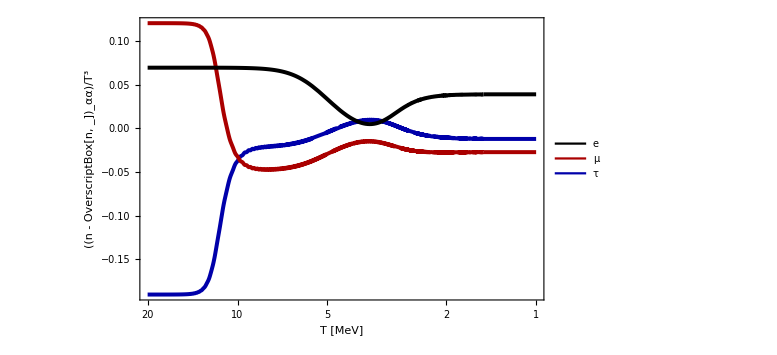

```mathematica
(*We provide initial conditions over (A,ϕ)*)
Aval=√2;
ϕval=π/3;
(*We translate from (A,ϕ) to (ξe,ξμ,ξτ)*)
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
(*We provide initial temperature (Tini), temperature at which oscillation average is taken (Tave), and final temperature (Tfinal)*)
(*Note we must provide Tini < Tave < Tfinal*)
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
(*We provide accuracy and precision settings for NDSolve*)
Accval=8;
Precval=8;
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
Adiabatic=False;
(*Execution time in seconds after which the solver switches to the adiabatic approximation*)
TimeoutAdiabatic=300; 


(*We call the functions that solve the system and generate plots*)
Fig3aFD=SolveFD["Fig3a",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"BDF",Adiabatic,TimeoutAdiabatic]
```

```mathematica
(*This benchmark the solver gets stuck around T=2MeV but fortunately the timeout switches to adiabatic and allows to reach Tave=1.5MeV*)
```

Starting evolution of the full system

Timeout of 300s reached at T= 1.94518 MeV → Switching to adiabatic V_s=0

System evolved until T_ave=1.5 MeV

Final ξe: 0.00529253

ΔN_eff: 0.000279101

Thermodynamics are output to: Results/Fig3b.dat

Total execution time: 5.725 min

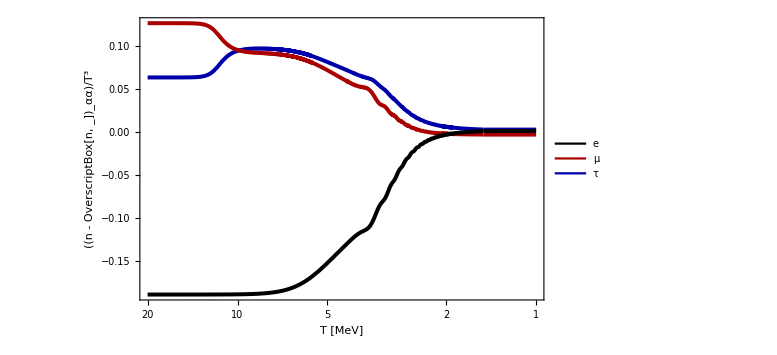

```mathematica
Aval=√2;
ϕval=ArcTan[-3,2];

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
Accval=7;
Precval=7;
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
Adiabatic=False;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig3bFD=SolveFD["Fig3b",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"BDF",Adiabatic,TimeoutAdiabatic]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.000213693

ΔN_eff: 3.04401×10^-8

Thermodynamics are output to: Results/Fig5a.dat

Total execution time: 4.044 s

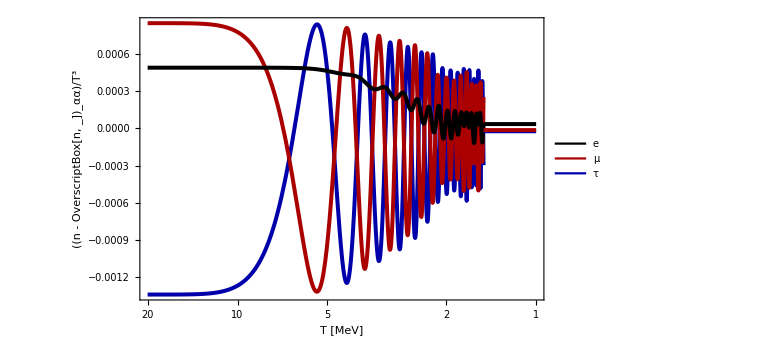

```mathematica
Aval=0.01;
ϕval=π/3;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
Accval=10;
Precval=10;
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
Adiabatic=False;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig5aFD=SolveFD["Fig5a",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"BDF",Adiabatic,TimeoutAdiabatic]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: -0.0250945

ΔN_eff: 0.0004281

Thermodynamics are output to: Results/Fig5b.dat

Total execution time: 1.452 min

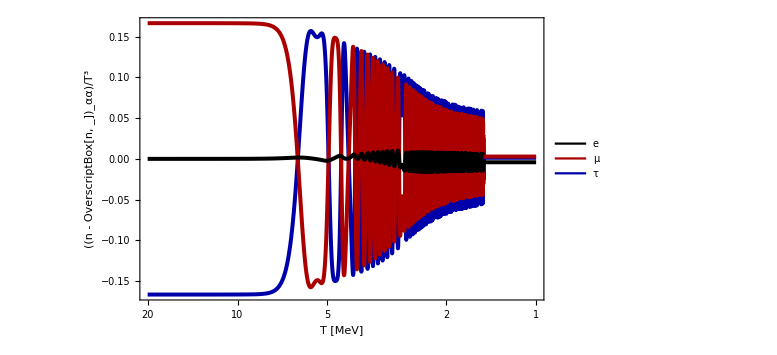

```mathematica
Aval=√2;
ϕval=π/2;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
Accval=10;
Precval=10;
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
Adiabatic=False;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig5bFD=SolveFD["Fig5b",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"BDF",Adiabatic,TimeoutAdiabatic]
```

Starting evolution of the full system

Timeout of 300s reached at T= 1.51996 MeV → Switching to adiabatic V_s=0

System evolved until T_ave=1.5 MeV

Final ξe: 0.215112

ΔN_eff: 0.030906

Thermodynamics are output to: Results/Fig6a.dat

Total execution time: 5.438 min

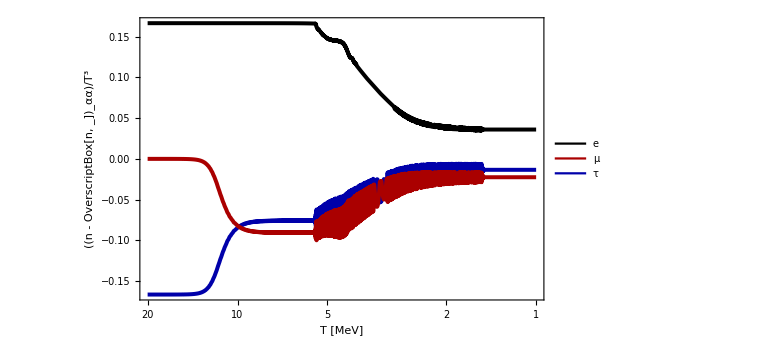

```mathematica
Aval=√2;
ϕval=0;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
Accval=8;
Precval=8;
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
Adiabatic=False;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig6aFD=SolveFD["Fig6a",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"BDF",Adiabatic,TimeoutAdiabatic]
```

## Benchmarks of the paper with damping collisions

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.00007644

ΔN_eff: 6.18879×10^-9

Thermodynamics are output to: Results/Fig5aD.dat

Total execution time: 2.166 s

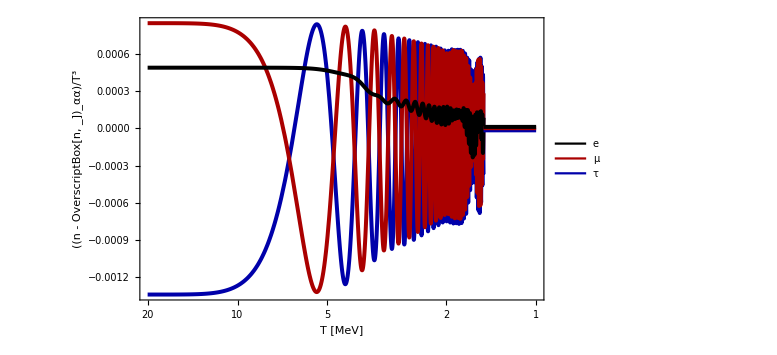

```mathematica
Aval=0.01;
ϕval=π/3;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
Accval=10;
Precval=10;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig5aD=SolveDamping["Fig5aD",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"BDF",False,TimeoutAdiabatic]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: -0.019074

ΔN_eff: 0.000248129

Thermodynamics are output to: Results/Fig5bD.dat

Total execution time: 18.93 s

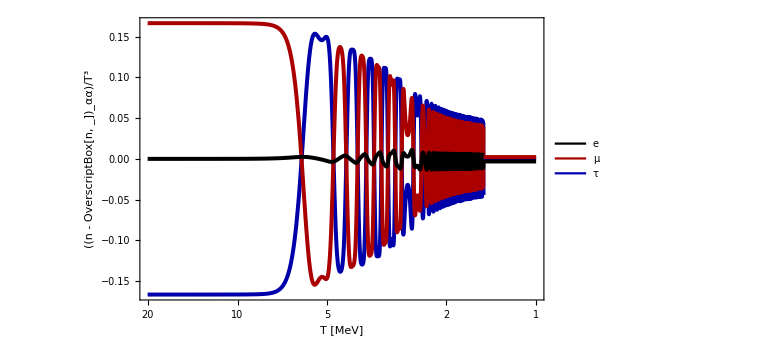

```mathematica
Aval=√2;
ϕval=π/2;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
Accval=10;
Precval=10;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig5bD=SolveDamping["Fig5bD",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"BDF",False,TimeoutAdiabatic]
```

```mathematica
(*These benchmarks work better with StiffnessSwitching than with BDF*)
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.0120649

ΔN_eff: 0.0000982504

Thermodynamics are output to: Results/Fig10a.dat

Total execution time: 1.318 min

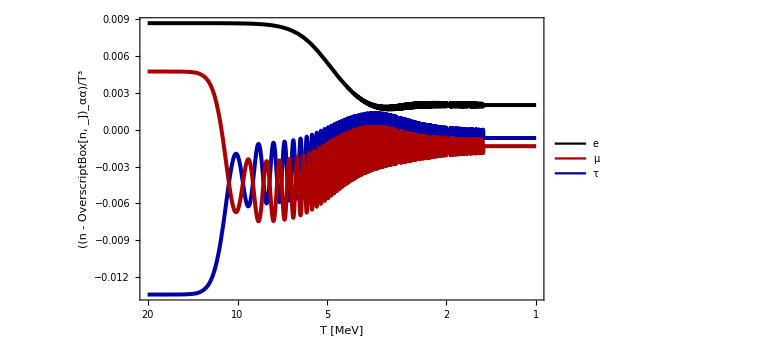

```mathematica
Aval=0.1;
ϕval=0.5;
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
Accval=8;
Precval=8;
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
Adiabatic=False;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig10a=SolveDamping["Fig10a",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"StiffnessSwitching",Adiabatic,TimeoutAdiabatic]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.122709

ΔN_eff: 0.0101872

Thermodynamics are output to: Results/Fig10b.dat

Total execution time: 1.299 min

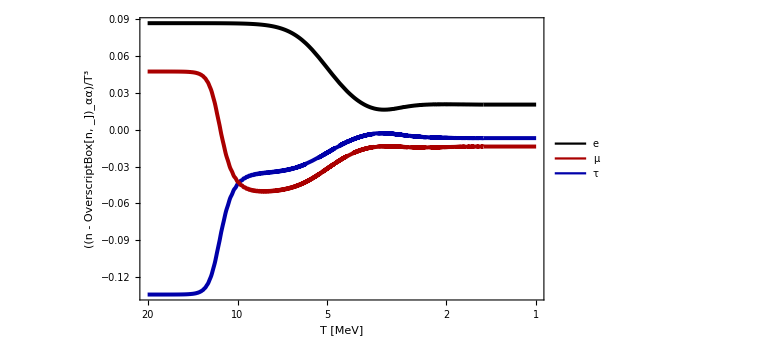

```mathematica
Aval=1;
ϕval=0.5;
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;(*Note that always Tfinal < Tave*)
Accval=7;
Precval=7;
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
Adiabatic=False;
TimeoutAdiabatic=300; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig10b=SolveDamping["Fig10b",ξeini,ξμini,ξτini,Tini,Tave,Tfinal,Accval,Precval,"StiffnessSwitching",Adiabatic,TimeoutAdiabatic]
```

## Comparisons

## Comparison stefan

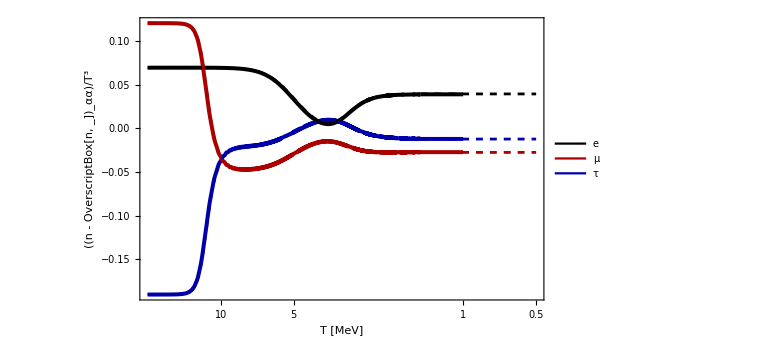

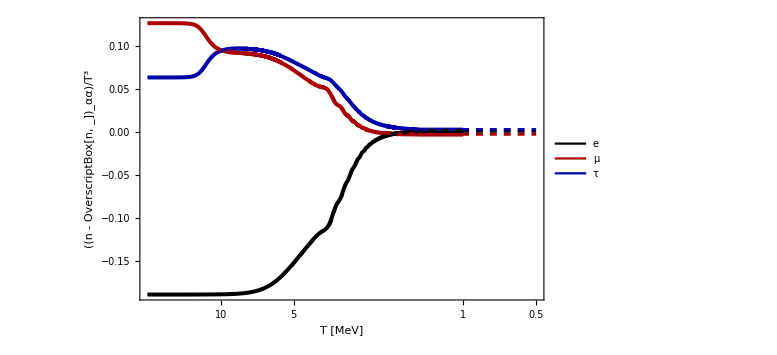

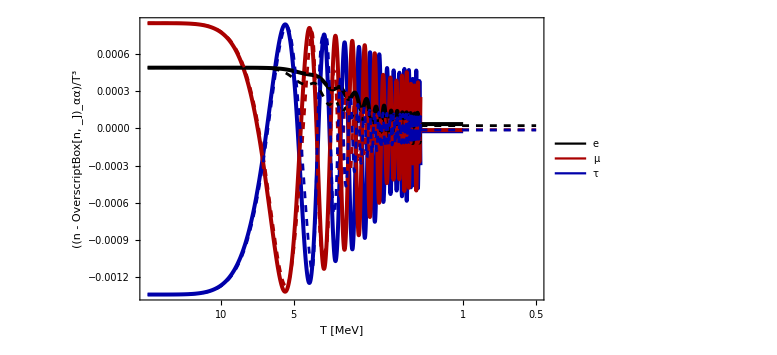

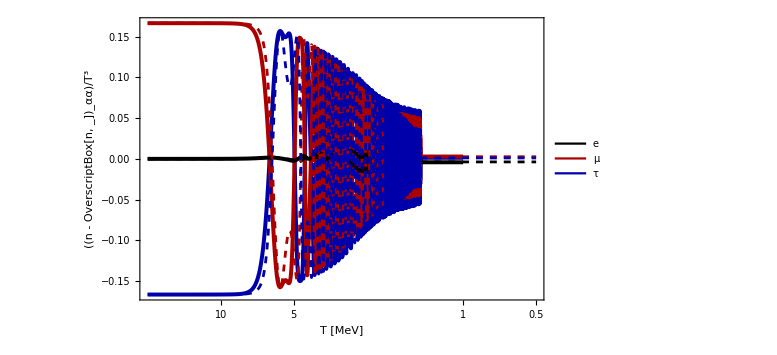

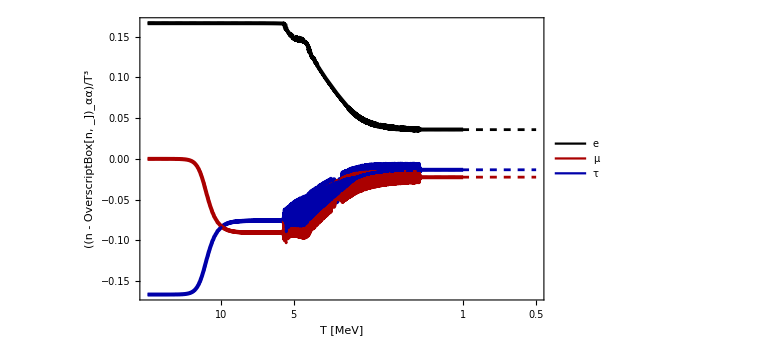

```mathematica
(*with m_e for Stefan*)
dat1=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_regular.dat"];
dat2=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_xie_final_0.dat"];
dat3=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_slowness_smallA.dat"];
dat4=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_xie_ini_0.dat"];
dat5=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_ximu_ini_0.dat"];


Plot3aStefanDashed=ListLinePlot[{Transpose[{dat1[[All,1]], dat1[[All,2]]}],Transpose[{dat1[[All,1]], dat1[[All,3]]}],Transpose[{dat1[[All,1]],dat1[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->{{20,1},{Automatic,Automatic}}];

Plot3bStefanDashed=ListLinePlot[{Transpose[{dat2[[All,1]], dat2[[All,2]]}],Transpose[{dat2[[All,1]], dat2[[All,3]]}],Transpose[{dat2[[All,1]],dat2[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->Full];
Plot5aStefanDashed=ListLinePlot[{Transpose[{dat3[[All,1]], dat3[[All,2]]}],Transpose[{dat3[[All,1]], dat3[[All,3]]}],Transpose[{dat3[[All,1]],dat3[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->{{20,1},{Automatic,Automatic}}];

Plot5bStefanDashed=ListLinePlot[{Transpose[{dat4[[All,1]], dat4[[All,2]]}],Transpose[{dat4[[All,1]], dat4[[All,3]]}],Transpose[{dat4[[All,1]],dat4[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->Full];
Plot6aStefanDashed=ListLinePlot[{Transpose[{dat5[[All,1]], dat5[[All,2]]}],Transpose[{dat5[[All,1]], dat5[[All,3]]}],Transpose[{dat5[[All,1]],dat5[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->Full];

Show[Fig3aFD,Plot3aStefanDashed]
Show[Fig3bFD,Plot3bStefanDashed]
Show[Fig5aFD,Plot5aStefanDashed]
Show[Fig5bFD,Plot5bStefanDashed]
Show[Fig6aFD,Plot6aStefanDashed]
```

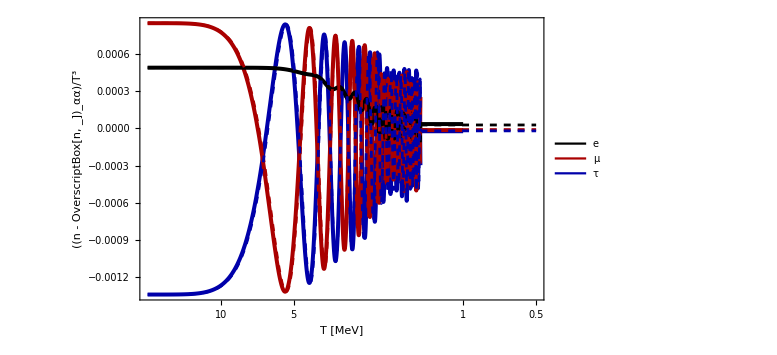

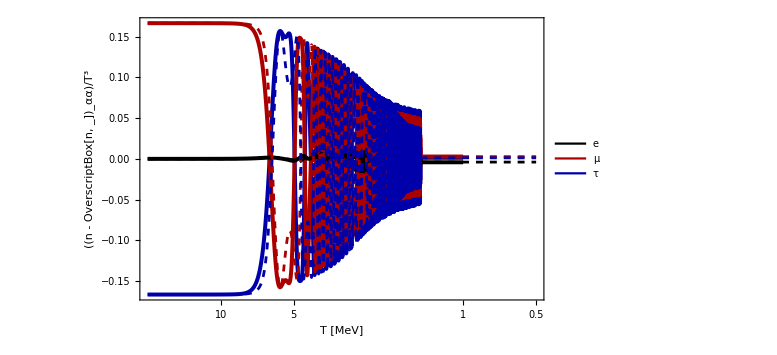

```mathematica
(*without m_e for Stefan*)
dat3=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_slowness_smallA_fullC_no_me.dat"];
dat4=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_xie_ini_0_fullC_no_me.dat"];


Plot5aStefanDashedNome=ListLinePlot[{Transpose[{dat3[[All,1]], dat3[[All,2]]}],Transpose[{dat3[[All,1]], dat3[[All,3]]}],Transpose[{dat3[[All,1]],dat3[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->{{20,1},{Automatic,Automatic}}];

Plot5bStefanDashedNome=ListLinePlot[{Transpose[{dat4[[All,1]], dat4[[All,2]]}],Transpose[{dat4[[All,1]], dat4[[All,3]]}],Transpose[{dat4[[All,1]],dat4[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->Full];

Show[Fig5aFD,Plot5aStefanDashedNome]
Show[Fig5bFD,Plot5bStefanDashedNome]
```

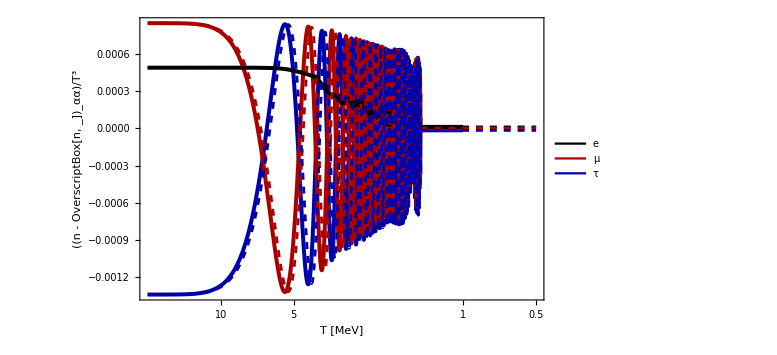

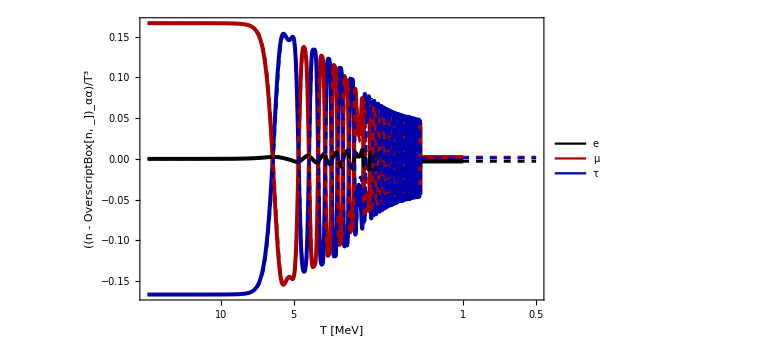

```mathematica
dat3=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_slowness_smallA_dampingapprox.dat"];
dat4=Import[NotebookDirectory[]<>"Plot_Comparison/Results_Stefan/Benchmark_xie_ini_0_dampingapprox.dat"];


Plot5aDampingStefanDashed=ListLinePlot[{Transpose[{dat3[[All,1]], dat3[[All,2]]}],Transpose[{dat3[[All,1]], dat3[[All,3]]}],Transpose[{dat3[[All,1]],dat3[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->{{20,1},{Automatic,Automatic}}];

Plot5bDampingStefanDashed=ListLinePlot[{Transpose[{dat4[[All,1]], dat4[[All,2]]}],Transpose[{dat4[[All,1]], dat4[[All,3]]}],Transpose[{dat4[[All,1]],dat4[[All,4]]}]},ScalingFunctions->{{-Log[#]&,Exp[-#]&},None},PlotStyle->{{Black,Dashed},{Darker@Red,Dashed},{Darker@Blue,Dashed}},PlotRange->Full];

Show[Fig5aD,Plot5aDampingStefanDashed]
Show[Fig5bD,Plot5bDampingStefanDashed]
```

## Final time

```mathematica
tf=Now;
tf-ti
```

17.8567 min